{1001,2}

17.6714

{1001}

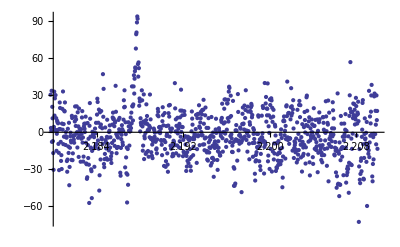

```mathematica
y=Flatten[Import["~////y.csv"]];
v=Flatten[Import["~//v.csv"]];
data=Table[{v[[i]],y[[i]]},{i,1,1001}];
Dimensions[data]
Δ=StandardDeviation[y[[1;;241]]]
weights=Table[1/(Δ^2),{i,1,1001}];
Dimensions[weights]
ListPlot[data,PlotRange->All]
```

FittedModel[-3.04192+79.0472 ⅇ^(-1.07474×10^7 (-«19»+x)^2)]

{P1→79.0472,μ1→2.1877,σ1→0.000215692,d→-3.04192}

-3.04192+79.0472 ⅇ^(-1.07474×10^7 (-2.1877+x)^2)

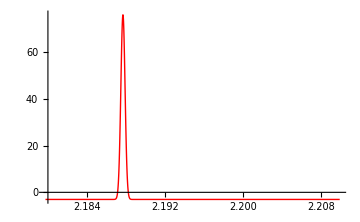
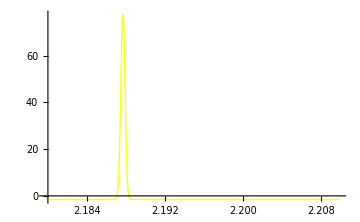
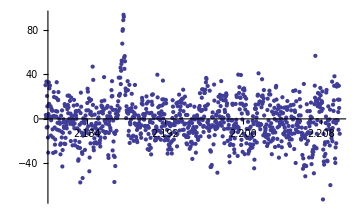

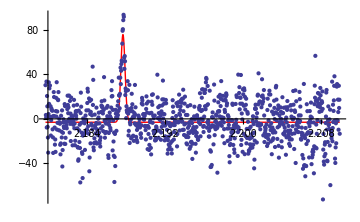

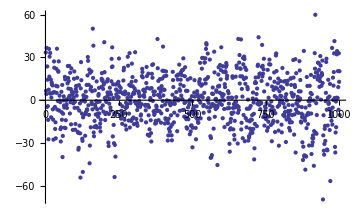

0.971904

{P1→79.0472,μ1→2.1877,σ1→0.000215692,d→-3.04192}

| Estimate | Standard Error | Confidence Interval
P1 | 79.0472 | 6.10993 | {67.0574,91.037}
μ1 | 2.1877 | 0.0000188329 | {2.18766,2.18774}
σ1 | 0.000215692 | 0.0000190838 | {0.000178243,0.000253141}
d | -3.04192 | 0.561373 | {-4.14353,-1.94031}

{6.10993,0.0000188329,0.0000190838,0.561373}

| DF | SS | MS
Model | 4 | 250.748 | 62.687
Error | 997 | 968.988 | 0.971904
Uncorrected Total | 1001 | 1219.74 | 
Corrected Total | 1000 | 1211.06 |

```mathematica
Gauss[x_,A_,μ_,σ_]=A √(2 π)σ PDF[NormalDistribution[μ,σ],x];
function=d+Gauss[x,P1,μ1,σ1];+ Gauss[x,P2,μ2,σ2] ;
model=NonlinearModelFit[data,function,{P1,μ1,σ1(*,P2,μ2,σ2*),d},x,Weights->weights, MaxIterations->1000];
nlm=model
par=nlm["BestFitParameters"]
g1[x_]=Gauss[x,P1,μ1,σ1] + d/2 /.par;
g2[x_]=Gauss[x,P2,μ2,σ2] + d/2 /.par;
gauss[x_]=Normal[nlm]
p1:=Plot[gauss[x],{x,Min[v],Max[v]},PlotRange->All,PlotStyle->{Thick,Red},ImageSize->Medium]
p2:=Plot[{g1[x],g2[x]},{x,Min[v],Max[v]},PlotRange->All,PlotStyle->{Yellow,Green},PlotStyle->Thick,ImageSize->Medium]
datplot:=ListPlot[data,PlotRange->All,ImageSize->Medium]
{p1,p2,datplot}
Show[p1,datplot]
ListPlot[nlm["FitResiduals"]]
nlm["EstimatedVariance"]
nlm["BestFitParameters"]
nlm["ParameterConfidenceIntervalTable"]
nlm["ParameterErrors"]
nlm["ANOVATable"]
```